# Forma canónica del grafo de transición en GPU (CUDA)

Clasificación de las reglas ECA por la forma canónica de su grafo de transición en espacios periódicos de  células, para . Se usa una regla por clase de inverso + espejo (88 reglas): las reglas de una misma clase tienen grafos isomorfos, así que el número de formas canónicas distintas es el mismo que con las 256.

## Método

Es el mismo proceso de la sección Isomorfismo y forma canónica del paper, adaptado a la GPU:

1. Sucesores (GPU). Un hilo por configuración; la regla se aplica con operaciones de bits sobre la palabra de  bits.

2. Grado de entrada (GPU). Con Compile`AtomicUpdate (suma atómica).

3. Poda desde los Jardín del Edén (GPU). Cola de Kahn por niveles. El código de cada nodo es un hash de 64 bits del multiconjunto de los códigos de sus predecesores: cada hijo suma  de forma atómica al acumulador del padre, y el código del padre es  (splitmix64). La suma es conmutativa, así que el código no depende de las etiquetas, igual que la lista ordenada del paper. Los niveles grandes se lanzan con toda la malla; las cadenas largas de niveles pequeños las recorre un solo bloque de 1024 hilos sincronizado con SynchronizeThreads (__syncthreads).

4. Ciclos (GPU + CPU compilado). Los nodos que nunca entraron a la cola son los de los ciclos. La GPU los compacta junto con el código del árbol que cuelga de cada uno; en CPU (FunctionCompilepaclet:ref/FunctionCompilehttps://reference.wolfram.com/language/ref/FunctionCompile.html) cada ciclo se codifica con su rotación lexicográficamente mínima (algoritmo de dos punteros: O(L) en tiempo y O(1) en memoria extra). La forma canónica es la lista ordenada de los códigos de los ciclos.

Validación: para  y las 256 reglas, la partición obtenida es idéntica a la de CanonFuncGraph (forma canónica exacta con listas anidadas).Límite. La GPU necesita unos 20 bytes por configuración: con 16 GB (RTX 5080) el máximo es  (~11.9 GB);  requeriría ~21 GB.Nota sobre la tarjeta. Mathematica lee la capacidad de cómputo 12.0 de la RTX 5080 como sm_12; por eso cada kernel se compila con "CUDAArchitecture"->"sm_120" explícito.

## Funciones

```mathematica
(* Constantes del hash (splitmix64), como enteros con signo *)
sgn64[u_]:=If[u>=2^63,u-2^64,u];
{mixA,mixB,kF,kG,kC}=sgn64 /@ {16^^bf58476d1ce4e5b9,16^^94d049bb133111eb,
    16^^9e3779b97f4a7c15,16^^d1b54a32d192ed03,16^^8cb92ba72f3d8dd7};

cudaSession=StartExternalSession["CUDA"];
cudaFn[f_]:=ExternalEvaluate[cudaSession,ExternalOperation["Function",f,"CUDAArchitecture"->"sm_120"]];
```

### Kernels de la poda

```mathematica
(* Sucesor de cada configuracion (ECA, frontera periodica) y reinicio de pend/acc *)
kSucc=cudaFn[Function[{Typed[succ,"CArray"::["Integer32"]],Typed[pend,"CArray"::["Integer32"]],
    Typed[acc,"CArray"::["Integer64"]],Typed[rule,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},
   Module[{id,x,mask,l,r,nx,a,b,c},
    id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
    If[id<total,
     x=Cast[id,"UnsignedInteger64","CCast"];
     mask=Cast[total-1,"UnsignedInteger64","CCast"];
     l=BitAnd[BitOr[BitShiftRight[x,1],BitShiftLeft[x,n-1]],mask];
     r=BitAnd[BitOr[BitShiftLeft[x,1],BitShiftRight[x,n-1]],mask];
     nx=Cast[0,"UnsignedInteger64","CCast"];
     Do[If[BitAnd[BitShiftRight[rule,v],1]==1,
       a=If[BitAnd[v,4]!=0,l,BitXor[l,mask]];
       b=If[BitAnd[v,2]!=0,x,BitXor[x,mask]];
       c=If[BitAnd[v,1]!=0,r,BitXor[r,mask]];
       nx=BitOr[nx,BitAnd[BitAnd[a,b],c]]],{v,0,7}];
     ToRawPointer[succ,id,Cast[nx,"Integer32","CCast"]];
     ToRawPointer[pend,id,Cast[0,"Integer32","CCast"]];
     ToRawPointer[acc,id,Cast[0,"Integer64","CCast"]]];]]];

(* Grado de entrada *)
kDeg=cudaFn[Function[{Typed[succ,"CArray"::["Integer32"]],Typed[pend,"CArray"::["Integer32"]],Typed[total,"MachineInteger"]},
   Module[{id},
    id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
    If[id<total,Compile`AtomicUpdate[pend,FromRawPointer[succ,id],"Plus",Cast[1,"Integer32","CCast"]]];]]];

(* Cola inicial: Jardines del Eden *)
kSeed=cudaFn[Function[{Typed[pend,"CArray"::["Integer32"]],Typed[q,"CArray"::["Integer32"]],Typed[cnt,"CArray"::["Integer32"]],Typed[total,"MachineInteger"]},
   Module[{id,i},
    id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
    If[id<total&&FromRawPointer[pend,id]==Cast[0,"Integer32","CCast"],
     i=Compile`AtomicUpdate[cnt,0,"Plus",Cast[1,"Integer32","CCast"]];
     ToRawPointer[q,i,Cast[id,"Integer32","CCast"]]];]]];

(* Un nivel de la poda: cada nodo de la cola calcula su codigo y lo suma al de su sucesor *)
kStep=With[{mixA=mixA,mixB=mixB,kF=kF,kG=kG},cudaFn[Function[{Typed[q,"CArray"::["Integer32"]],Typed[succ,"CArray"::["Integer32"]],
    Typed[pend,"CArray"::["Integer32"]],Typed[acc,"CArray"::["Integer64"]],Typed[cnt,"CArray"::["Integer32"]],
    Typed[start,"MachineInteger"],Typed[len,"MachineInteger"]},
   Module[{id,v,u,z,old,i},
    id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
    If[id<len,
     v=FromRawPointer[q,start+id];
     u=FromRawPointer[succ,v];
     (* F: codigo del nodo a partir de la suma de sus hijos *)
     z=Cast[FromRawPointer[acc,v],"UnsignedInteger64","CCast"]+Cast[kF,"UnsignedInteger64","CCast"];
     z=BitXor[z,BitShiftRight[z,30]]*Cast[mixA,"UnsignedInteger64","CCast"];
     z=BitXor[z,BitShiftRight[z,27]]*Cast[mixB,"UnsignedInteger64","CCast"];
     z=BitXor[z,BitShiftRight[z,31]];
     (* G: contribucion al multiconjunto del padre *)
     z=BitXor[z,Cast[kG,"UnsignedInteger64","CCast"]];
     z=BitXor[z,BitShiftRight[z,30]]*Cast[mixA,"UnsignedInteger64","CCast"];
     z=BitXor[z,BitShiftRight[z,27]]*Cast[mixB,"UnsignedInteger64","CCast"];
     z=BitXor[z,BitShiftRight[z,31]];
     Compile`AtomicUpdate[acc,u,"Plus",Cast[z,"Integer64","CCast"]];
     old=Compile`AtomicUpdate[pend,u,"Subtract",Cast[1,"Integer32","CCast"]];
     If[old==Cast[1,"Integer32","CCast"],
      i=Compile`AtomicUpdate[cnt,0,"Plus",Cast[1,"Integer32","CCast"]];
      ToRawPointer[q,i,u]]];]]]];

(* Avanza el rango del nivel actual en la GPU: cnt = {cola, ciclos, inicio, fin, niveles, ...} *)
kAdvance=cudaFn[Function[{Typed[cnt,"CArray"::["Integer32"]],Typed[inc,"MachineInteger"]},
   Module[{},
    If[LibraryFunction["ThreadID.x"][]==0&&LibraryFunction["BlockID.x"][]==0,
     ToRawPointer[cnt,2,FromRawPointer[cnt,3]];
     ToRawPointer[cnt,3,FromRawPointer[cnt,0]];
     ToRawPointer[cnt,4,FromRawPointer[cnt,4]+Cast[inc,"Integer32","CCast"]]];]]];

(* Niveles pequenos: un solo bloque de 1024 hilos recorre muchos niveles en un lanzamiento,
   sincronizando con __syncthreads; regresa cuando el nivel crece mas que thr o se vacia la cola *)
kStepSmall=With[{mixA=mixA,mixB=mixB,kF=kF,kG=kG},cudaFn[Function[{Typed[q,"CArray"::["Integer32"]],Typed[succ,"CArray"::["Integer32"]],
    Typed[pend,"CArray"::["Integer32"]],Typed[acc,"CArray"::["Integer64"]],Typed[cnt,"CArray"::["Integer32"]],
    Typed[thr,"MachineInteger"]},
   Module[{tid,s,e,go=True,j,v,u,z,old,i},
    tid=LibraryFunction["ThreadID.x"][];
    While[go,
     s=Cast[Compile`AtomicUpdate[cnt,2,"Plus",Cast[0,"Integer32","CCast"]],"MachineInteger"];
     e=Cast[Compile`AtomicUpdate[cnt,3,"Plus",Cast[0,"Integer32","CCast"]],"MachineInteger"];
     If[e==s||e-s>thr,
      go=False,
      j=s+tid;
      While[j<e,
       v=FromRawPointer[q,j];
       u=FromRawPointer[succ,v];
       z=Cast[FromRawPointer[acc,v],"UnsignedInteger64","CCast"]+Cast[kF,"UnsignedInteger64","CCast"];
       z=BitXor[z,BitShiftRight[z,30]]*Cast[mixA,"UnsignedInteger64","CCast"];
       z=BitXor[z,BitShiftRight[z,27]]*Cast[mixB,"UnsignedInteger64","CCast"];
       z=BitXor[z,BitShiftRight[z,31]];
       z=BitXor[z,Cast[kG,"UnsignedInteger64","CCast"]];
       z=BitXor[z,BitShiftRight[z,30]]*Cast[mixA,"UnsignedInteger64","CCast"];
       z=BitXor[z,BitShiftRight[z,27]]*Cast[mixB,"UnsignedInteger64","CCast"];
       z=BitXor[z,BitShiftRight[z,31]];
       Compile`AtomicUpdate[acc,u,"Plus",Cast[z,"Integer64","CCast"]];
       old=Compile`AtomicUpdate[pend,u,"Subtract",Cast[1,"Integer32","CCast"]];
       If[old==Cast[1,"Integer32","CCast"],
        i=Compile`AtomicUpdate[cnt,0,"Plus",Cast[1,"Integer32","CCast"]];
        ToRawPointer[q,i,u]];
       j=j+1024];
      LibraryFunction["SynchronizeThreads"][];
      If[tid==0,
       Compile`AtomicUpdate[cnt,2,"Plus",Cast[e-s,"Integer32","CCast"]];
       Compile`AtomicUpdate[cnt,3,"Plus",Compile`AtomicUpdate[cnt,0,"Plus",Cast[0,"Integer32","CCast"]]-Cast[e,"Integer32","CCast"]];
       Compile`AtomicUpdate[cnt,4,"Plus",Cast[1,"Integer32","CCast"]]];
      LibraryFunction["SynchronizeThreads"][]]];]]]];
```

### Kernels de los ciclos

```mathematica
(* Nodos de ciclo: indice compacto (guardado como -(i+1) en pend) y codigo del arbol que cuelga *)
kCycA=With[{mixA=mixA,mixB=mixB,kF=kF},cudaFn[Function[{Typed[pend,"CArray"::["Integer32"]],Typed[acc,"CArray"::["Integer64"]],
    Typed[cnt,"CArray"::["Integer32"]],Typed[total,"MachineInteger"]},
   Module[{id,i,z},
    id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
    If[id<total&&FromRawPointer[pend,id]>Cast[0,"Integer32","CCast"],
     i=Compile`AtomicUpdate[cnt,1,"Plus",Cast[1,"Integer32","CCast"]];
     ToRawPointer[pend,id,-i-Cast[1,"Integer32","CCast"]];
     z=Cast[FromRawPointer[acc,id],"UnsignedInteger64","CCast"]+Cast[kF,"UnsignedInteger64","CCast"];
     z=BitXor[z,BitShiftRight[z,30]]*Cast[mixA,"UnsignedInteger64","CCast"];
     z=BitXor[z,BitShiftRight[z,27]]*Cast[mixB,"UnsignedInteger64","CCast"];
     z=BitXor[z,BitShiftRight[z,31]];
     ToRawPointer[acc,id,Cast[z,"Integer64","CCast"]]];]]]];

(* Sucesor de cada nodo de ciclo en indices compactos (se escribe en la cola, ya libre) *)
kCycB=cudaFn[Function[{Typed[succ,"CArray"::["Integer32"]],Typed[pend,"CArray"::["Integer32"]],Typed[nxt,"CArray"::["Integer32"]],Typed[total,"MachineInteger"]},
   Module[{id,p},
    id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
    If[id<total,
     p=FromRawPointer[pend,id];
     If[p<Cast[0,"Integer32","CCast"],
      ToRawPointer[nxt,-p-Cast[1,"Integer32","CCast"],-FromRawPointer[pend,FromRawPointer[succ,id]]-Cast[1,"Integer32","CCast"]]]];]]];

(* Codigos de los nodos de ciclo con indice en [off, off+len), por bloques *)
kCycH=cudaFn[Function[{Typed[pend,"CArray"::["Integer32"]],Typed[acc,"CArray"::["Integer64"]],Typed[h,"CArray"::["Integer64"]],
    Typed[off,"MachineInteger"],Typed[len,"MachineInteger"],Typed[total,"MachineInteger"]},
   Module[{id,i},
    id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
    If[id<total,
     i=-FromRawPointer[pend,id]-1;
     If[i>=off&&i<off+len,ToRawPointer[h,i-off,FromRawPointer[acc,id]]]];]]];
```

### Rotación mínima de cada ciclo (CPU compilado)

```mathematica
cycleCodesC=With[{mixA=mixA,mixB=mixB,kC=kC},FunctionCompile[Function[{Typed[nxt,"NumericArray"::["Integer32",1]],Typed[h,"NumericArray"::["Integer64",1]],Typed[c,"MachineInteger"]},Module[{mark,nc=0,lmax=0,len,w,seq,k,i,j,a,b,code,codes,z,e,ci=0,m,t},mark=CreateTypeInstance["CArray"::["Integer8"],c];Do[ToRawPointer[mark,t,Cast[0,"Integer8","CCast"]],{t,0,c-1}];Do[If[FromRawPointer[mark,s-1]==Cast[0,"Integer8","CCast"],len=0;w=s;While[FromRawPointer[mark,w-1]==Cast[0,"Integer8","CCast"],ToRawPointer[mark,w-1,Cast[1,"Integer8","CCast"]];len++;w=nxt[[w]]+1];nc++;If[len>lmax,lmax=len]],{s,c}];seq=ConstantArray[0,lmax];codes=ConstantArray[0,nc];Do[If[FromRawPointer[mark,s-1]==Cast[1,"Integer8","CCast"],len=0;w=s;While[FromRawPointer[mark,w-1]==Cast[1,"Integer8","CCast"],ToRawPointer[mark,w-1,Cast[2,"Integer8","CCast"]];len++;seq[[len]]=h[[w]];w=nxt[[w]]+1];i=0;j=1;k=0;While[i<len&&j<len&&k<len,a=i+k;If[a>=len,a-=len];b=j+k;If[b>=len,b-=len];If[seq[[a+1]]==seq[[b+1]],k++,If[seq[[a+1]]>seq[[b+1]],i=i+k+1,j=j+k+1];If[i==j,j++];k=0]];k=Min[i,j];Native`UncheckedBlock[z=Cast[len,"UnsignedInteger64","CCast"]+Cast[kC,"UnsignedInteger64","CCast"];Do[e=Cast[seq[[Mod[k+m,len]+1]],"UnsignedInteger64","CCast"];z=BitXor[z,e]+Cast[kC,"UnsignedInteger64","CCast"];z=BitXor[z,BitShiftRight[z,30]]*Cast[mixA,"UnsignedInteger64","CCast"];z=BitXor[z,BitShiftRight[z,27]]*Cast[mixB,"UnsignedInteger64","CCast"];z=BitXor[z,BitShiftRight[z,31]],{m,0,len-1}];code=Cast[z,"Integer64","CCast"]];ci++;codes[[ci]]=code],{s,c}];DeleteObject[mark];codes]]]];
```

### Forma canónica de una regla

```mathematica
zerosNA[type_,total_]:=Module[{z=NumericArray[ConstantArray[0,Min[total,2^20]],type]},
   While[Length[z]<total,z=Join[z,z]]; z];
$chunk=2^26;
$smallLevel=16384;

(* Reserva de memoria en GPU para un tamano n (se reutiliza para todas las reglas) *)
AllocateCanon[n_]:=Module[{total=2^n,z32},
   z32=zerosNA["Integer32",total];
   <|"n"->n,"N"->total,"succ"->GPUArray[z32],"pend"->GPUArray[z32],"q"->GPUArray[z32],
    "acc"->GPUArray[zerosNA["Integer64",total]],"h"->GPUArray[zerosNA["Integer64",Min[total,$chunk]]]|>];

CanonicalFormGPU[rule_Integer,buf_Association]:=Module[{n=buf["n"],total=buf["N"],cnt,start=0,end,height=0,len,
    nGoE,c,nxt,h,codes},
   kSucc[buf["succ"],buf["pend"],buf["acc"],rule,n,total];
   kDeg[buf["succ"],buf["pend"],total];
   cnt=GPUArray[NumericArray[ConstantArray[0,8],"Integer32"]];
   kSeed[buf["pend"],buf["q"],cnt,total];
   kAdvance[cnt,0,"GridDimensions"->1,"BlockDimensions"->1];
   nGoE=Normal[NumericArray[cnt]][[4]];
   While[({start,end}=Normal[NumericArray[cnt]][[3 ;; 4]]; end>start),
    len=end-start;
    If[len>$smallLevel,
     kStep[buf["q"],buf["succ"],buf["pend"],buf["acc"],cnt,start,len,
      "GridDimensions"->Quotient[len-1,256]+1,"BlockDimensions"->256];
     kAdvance[cnt,1,"GridDimensions"->1,"BlockDimensions"->1],
     kStepSmall[buf["q"],buf["succ"],buf["pend"],buf["acc"],cnt,$smallLevel,
      "GridDimensions"->1,"BlockDimensions"->1024]]];
   {end,height}=Normal[NumericArray[cnt]][[{1,5}]];
   c=total-end;
   kCycA[buf["pend"],buf["acc"],cnt,total];
   kCycB[buf["succ"],buf["pend"],buf["q"],total];
   h=Join @@ Table[
      kCycH[buf["pend"],buf["acc"],buf["h"],off,Min[$chunk,c-off],total];
      Take[NumericArray[buf["h"]],Min[$chunk,c-off]],{off,0,c-1,$chunk}];
   nxt=NumericArray[buf["q"]];
   codes=Sort[cycleCodesC[nxt,h,c]];
   <|"Rule"->rule,"n"->n,"GardenOfEden"->nGoE,"Height"->height,"CycleNodes"->c,
    "Cycles"->Length[codes],"Canonical"->Hash[codes]|>];
```

### Las 88 reglas representantes

Mínimo de cada clase bajo espejo e inverso (complemento de estados).

```mathematica
mirrorRule[r_]:=Sum[BitGet[r,4 BitGet[v,0]+2 BitGet[v,1]+BitGet[v,2]] 2^v,{v,0,7}];
complementRule[r_]:=Sum[(1-BitGet[r,7-v]) 2^v,{v,0,7}];
ecaReps=Union[Table[Min[r,mirrorRule[r],complementRule[r],mirrorRule[complementRule[r]]],{r,0,255}]];
Length[ecaReps]
```

88

## Experimento: n = 1, …, 29

Cada tamaño se guarda en canonical_form_gpu_data.wl al terminar, así que si la corrida se interrumpe continúa desde el último  completo.

```mathematica
nMax=29;
dataFile=FileNameJoin[{Quiet@Check[NotebookDirectory[],Directory[]],"canonical_form_gpu_data.wl"}];
results=If[FileExistsQ[dataFile],Get[dataFile],<||>];
Do[If[! KeyExistsQ[results,n],
   Module[{buf=AllocateCanon[n],rows,t},
    t=First@AbsoluteTiming[rows=Table[CanonicalFormGPU[r,buf],{r,ecaReps}]];
    results[n]=<|"n"->n,"Seconds"->t,"Classes"->CountDistinct[rows[[All,"Canonical"]]],
      "Groups"->Values[GroupBy[rows,#["Canonical"] &,#[[All,"Rule"]] &]],"Rules"->rows|>;
    Put[results,dataFile]]],{n,1,nMax}];
Dataset[KeyTake[#,{"n","Classes","Seconds"}] & /@ Values[KeySort[results]]]
```

## Datos (Iconize)

```mathematica
canonData=;
```

## Gráfica

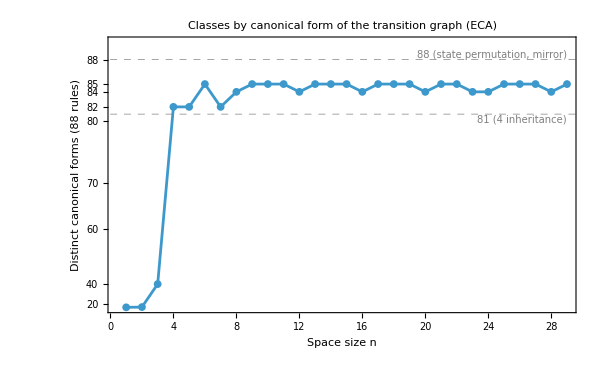

```mathematica
pts={#["n"],#["Classes"]}&/@Values[KeySort[canonData]];
yScale={#^3&,CubeRoot};
ListLinePlot[pts,PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct canonical forms (88 rules)"},FrameTicks->{{{20,40,60,70,80,82,84,85,88},Automatic},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],Epilog->{Text[Style["88 (state permutation, mirror)",10,Gray],{Max[pts[[All,1]]],yScale[[1]][88]},{1,-1.3}],Text[Style["81 (4 inheritance)",10,Gray],{Max[pts[[All,1]]],yScale[[1]][81]},{1,1.5}]},PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by canonical form of the transition graph (ECA)"]
```

## Cociente por rotaciones

Mismo experimento, pero sobre el grafo cociente por rotaciones (el de MakeGraphRot): cada nodo es una clase de configuraciones bajo rotación cíclica, representada por su rotación mínima, y la arista va de [x] a [F(x)]. Como F conmuta con la rotación, la arista está bien definida. El número de nodos baja de 2^n a unos 2^n/n (collares binarios): para n = 29 son 18 512 792 nodos y el cálculo de las 88 reglas tarda 36 s.

Solo cambia el cálculo de sucesores. kRepMark marca los representantes (un hilo por configuración, rotación mínima con n − 1 rotaciones de bits) y guarda su índice compacto; kSuccRot aplica la regla al representante, rota el resultado a su mínimo y busca su índice. La poda, los ciclos y la rotación mínima de cada ciclo usan los mismos kernels de arriba (kDeg, kSeed, kStep, kStepSmall, kCycA, kCycB, kCycH y cycleCodesC).

Validación: para n = 1..9 la partición de las 88 reglas coincide con la que se obtiene en CPU construyendo el grafo cociente y agrupando con IsomorphicGraphQ.

### Kernels del cociente

```mathematica
(* Representantes de las clases de rotación: configuraciones iguales a su rotación mínima. idx[x] guarda el índice compacto de cada representante *)
kRepMark=cudaFn[Function[{Typed[reps,TypeSpecifier["CArray"]["Integer32"]],Typed[idx,TypeSpecifier["CArray"]["Integer32"]],Typed[cnt,TypeSpecifier["CArray"]["Integer32"]],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},Module[{id,x,y,m,mask,k,i},id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];If[id<total,x=Cast[id,"UnsignedInteger64","CCast"];mask=Cast[total-1,"UnsignedInteger64","CCast"];m=x;y=x;k=1;While[k<n,y=BitAnd[BitOr[BitShiftLeft[y,1],BitShiftRight[y,n-1]],mask];If[y<m,m=y];k=k+1];If[m==x,i=Compile`AtomicUpdate[cnt,0,"Plus",Cast[1,"Integer32","CCast"]];ToRawPointer[reps,i,Cast[id,"Integer32","CCast"]];ToRawPointer[idx,id,i]]];]]];
(* Sucesor en el cociente: se aplica la regla al representante y se busca el índice de la rotación mínima del resultado *)
kSuccRot=cudaFn[Function[{Typed[succ,TypeSpecifier["CArray"]["Integer32"]],Typed[pend,TypeSpecifier["CArray"]["Integer32"]],Typed[acc,TypeSpecifier["CArray"]["Integer64"]],Typed[reps,TypeSpecifier["CArray"]["Integer32"]],Typed[idx,TypeSpecifier["CArray"]["Integer32"]],Typed[rule,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"],Typed[nr,"MachineInteger"]},Module[{id,x,mask,l,r,nx,a,b,c,y,m,k},id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];If[id<nr,x=Cast[FromRawPointer[reps,id],"UnsignedInteger64","CCast"];mask=Cast[total-1,"UnsignedInteger64","CCast"];l=BitAnd[BitOr[BitShiftRight[x,1],BitShiftLeft[x,n-1]],mask];r=BitAnd[BitOr[BitShiftLeft[x,1],BitShiftRight[x,n-1]],mask];nx=Cast[0,"UnsignedInteger64","CCast"];Do[If[BitAnd[BitShiftRight[rule,v],1]==1,a=If[BitAnd[v,4]!=0,l,BitXor[l,mask]];b=If[BitAnd[v,2]!=0,x,BitXor[x,mask]];c=If[BitAnd[v,1]!=0,r,BitXor[r,mask]];nx=BitOr[nx,BitAnd[BitAnd[a,b],c]]],{v,0,7}];m=nx;y=nx;k=1;While[k<n,y=BitAnd[BitOr[BitShiftLeft[y,1],BitShiftRight[y,n-1]],mask];If[y<m,m=y];k=k+1];ToRawPointer[succ,id,FromRawPointer[idx,Cast[m,"MachineInteger","CCast"]]];ToRawPointer[pend,id,Cast[0,"Integer32","CCast"]];ToRawPointer[acc,id,Cast[0,"Integer64","CCast"]]];]]];
```

### Forma canónica de una regla (cociente)

```mathematica
(* Los representantes solo dependen de n: se calculan una vez por tamaño *)
AllocateCanonRot[n_]:=Module[{total=2^n,cnt,reps,idx,nr,z32},reps=GPUArray[zerosNA["Integer32",total]];idx=GPUArray[zerosNA["Integer32",total]];cnt=GPUArray[NumericArray[ConstantArray[0,8],"Integer32"]];kRepMark[reps,idx,cnt,n,total];nr=First[Normal[NumericArray[cnt]]];reps=GPUArray[Take[NumericArray[reps],nr]];z32=zerosNA["Integer32",nr];<|"n"->n,"N"->nr,"total"->total,"reps"->reps,"idx"->idx,"succ"->GPUArray[z32],"pend"->GPUArray[z32],"q"->GPUArray[z32],"acc"->GPUArray[zerosNA["Integer64",nr]],"h"->GPUArray[zerosNA["Integer64",Min[nr,$chunk]]]|>];
(* Igual que CanonicalFormGPU, pero sobre los nr nodos del cociente *)
CanonicalFormRotGPU[rule_Integer,buf_Association]:=Module[{n=buf["n"],total=buf["N"],cnt,start=0,end,height=0,len,nGoE,c,nxt,h,codes},kSuccRot[buf["succ"],buf["pend"],buf["acc"],buf["reps"],buf["idx"],rule,n,buf["total"],total,"GridDimensions"->Quotient[total-1,256]+1,"BlockDimensions"->256];kDeg[buf["succ"],buf["pend"],total];cnt=GPUArray[NumericArray[ConstantArray[0,8],"Integer32"]];kSeed[buf["pend"],buf["q"],cnt,total];kAdvance[cnt,0,"GridDimensions"->1,"BlockDimensions"->1];nGoE=Normal[NumericArray[cnt]][[4]];While[{start,end}=Normal[NumericArray[cnt]][[3;;4]];end>start,len=end-start;If[len>$smallLevel,kStep[buf["q"],buf["succ"],buf["pend"],buf["acc"],cnt,start,len,"GridDimensions"->Quotient[len-1,256]+1,"BlockDimensions"->256];kAdvance[cnt,1,"GridDimensions"->1,"BlockDimensions"->1],kStepSmall[buf["q"],buf["succ"],buf["pend"],buf["acc"],cnt,$smallLevel,"GridDimensions"->1,"BlockDimensions"->1024]]];{end,height}=Normal[NumericArray[cnt]][[{1,5}]];c=total-end;kCycA[buf["pend"],buf["acc"],cnt,total];kCycB[buf["succ"],buf["pend"],buf["q"],total];h=Join@@Table[kCycH[buf["pend"],buf["acc"],buf["h"],off,Min[$chunk,c-off],total];Take[NumericArray[buf["h"]],Min[$chunk,c-off]],{off,0,c-1,$chunk}];nxt=NumericArray[buf["q"]];codes=Sort[cycleCodesC[nxt,h,c]];<|"Rule"->rule,"n"->n,"Nodes"->total,"GardenOfEden"->nGoE,"Height"->height,"CycleNodes"->c,"Cycles"->Length[codes],"Canonical"->Hash[codes]|>];
```

## Experimento con rotaciones: n = 1, …, 29

Cada tamaño se guarda en canonical_form_rot_gpu_data.wl; si el archivo existe, solo se calculan los tamaños que faltan. Requiere las celdas de Funciones y nMax de la sección del grafo completo.

```mathematica
dataFileRot=FileNameJoin[{Quiet[Check[NotebookDirectory[],Directory[]]],"canonical_form_rot_gpu_data.wl"}];
resultsRot=If[FileExistsQ[dataFileRot],Get[dataFileRot],<||>];
Do[If[!KeyExistsQ[resultsRot,n],Module[{buf=AllocateCanonRot[n],rows,t},t=First[AbsoluteTiming[rows=Table[CanonicalFormRotGPU[r,buf],{r,ecaReps}]]];resultsRot[n]=<|"n"->n,"Nodes"->buf["N"],"Seconds"->t,"Classes"->CountDistinct[rows[[All,"Canonical"]]],"Groups"->Values[GroupBy[rows,#["Canonical"]&,#[[All,"Rule"]]&]],"Rules"->rows|>;Put[resultsRot,dataFileRot]]],{n,1,nMax}];
Dataset[KeyTake[#,{"n","Nodes","Classes","Seconds"}]&/@Values[KeySort[resultsRot]]]
```

## Datos rotaciones (Iconize)

```mathematica
canonRotData=;
```

## Gráfica (rotaciones)

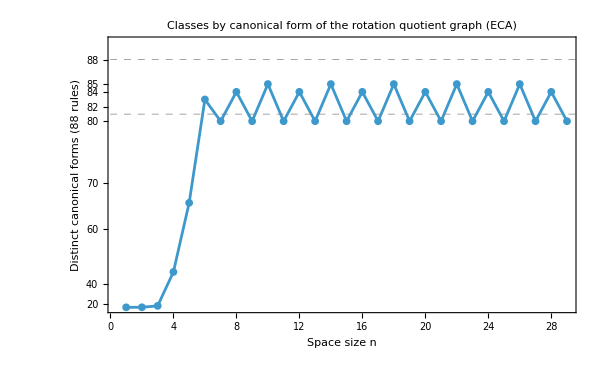

```mathematica
ptsRot={#["n"],#["Classes"]}&/@Values[KeySort[canonRotData]];
yScale={#^3&,CubeRoot};
ListLinePlot[ptsRot,PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct canonical forms (88 rules)"},FrameTicks->{{{20,40,60,70,80,82,84,85,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by canonical form of the rotation quotient graph (ECA)"]
```

## Gráfica combinada

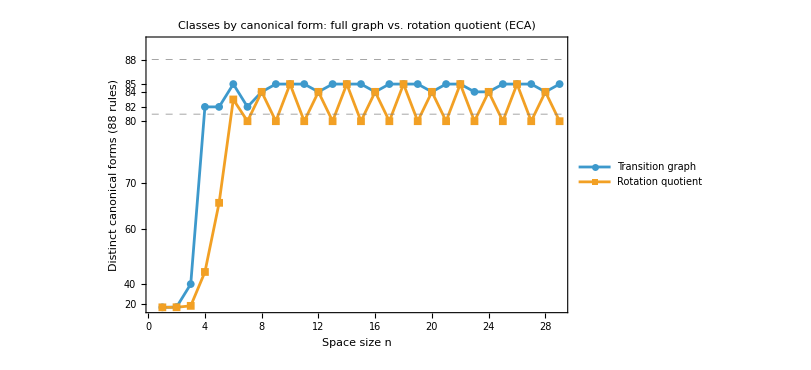

```mathematica
pts={#["n"],#["Classes"]}&/@Values[KeySort[canonData]];
ptsRot={#["n"],#["Classes"]}&/@Values[KeySort[canonRotData]];
yScale={#^3&,CubeRoot};
ListLinePlot[{pts,ptsRot},PlotMarkers->{Automatic,8},Frame->True,ScalingFunctions->{None,yScale},FrameLabel->{"Space size n","Distinct canonical forms (88 rules)"},FrameTicks->{{{20,40,60,70,80,82,84,85,88},{{81,Style["81 (4 inheritance)",10,Gray]},{88,Style["88 (state permutation, mirror)",10,Gray]}}},{Automatic,Automatic}},GridLines->{None,{81,88}},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[{"Transition graph","Rotation quotient"},{Right,Center}],PlotRange->{All,{0,90}},ImageSize->600,PlotLabel->"Classes by canonical form: full graph vs. rotation quotient (ECA)"]
```

## Resultados (rotaciones)

Clases por n: 3, 6, 16, 46, 66, 83 para n = 1..6. Desde n = 7 el número depende solo de n mod 4: 80 si n es impar, 85 si n ≡ 2 (mod 4) y 84 si 4 | n. Nunca se llega a 88, y combinando los 29 tamaños solo se obtienen 85 clases.

En todo n ≥ 6 se fusionan {12, 34}, {15, 51} y {170, 204}. Son pares que difieren en componer con el desplazamiento: 170 es el desplazamiento y 204 la identidad, 15 = ¬l y 51 = ¬c, 12 = ¬l ∧ c y 34 = ¬c ∧ r. En el cociente el desplazamiento es una rotación, es decir, la identidad, así que estas reglas no se pueden separar con ningún tamaño.

Fusiones adicionales (n ≥ 7): con n impar {3, 5}, {24, 46}, {60, 90}, {136, 160} y {10, 12, 34}; con n = 8, 16, 20 y 28 {105, 150}; con n = 12 y 24 {43, 142}. Las particiones del grafo completo y del cociente no están anidadas: con n impar (salvo n = 7) el cociente es más grueso que el grafo completo, pero con n par cada uno separa pares que el otro fusiona (por ejemplo, con n = 10 el grafo completo fusiona {15, 170} y el cociente los separa).

Combinando ambas formas canónicas en el mismo tamaño se obtienen las 88 clases con n = 6, 10, 12, 14, 18, 22, 24 y 26 (87 con n = 8, 16, 20 y 28). Es decir, un solo espacio de 6 células basta si se usan el grafo completo y su cociente por rotaciones, mientras que con el grafo completo solo se necesitan dos tamaños (n = 3 y 4).